```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

NotebookDirectory::nosv: The notebook obj is not saved.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File.

SetDirectory[$Failed]

## Lognormal σ^2=10^-2

```mathematica
npeak=16;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-2;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/100) π)

```mathematica
R3//N
```

4.11245

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/50)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];]
```

{4.84308,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
```

```mathematica
s2b=10^-1;
```

```mathematica
Normal[Series[Sinc''[E^lnk x]+2/(x E^lnk)Sinc'[E^lnk x],{x,0,0}]]
```

-1

```mathematica
1/x^2 D[(x^2 D[(b''[x]+2/x b'[x]), x]), x]//Simplify
```

(4 b^(3)[x])/x+b^(4)[x]

```mathematica
Normal[Series[Sinc''''[E^lnk x]+4/(x E^lnk)Sinc'''[E^lnk x],{x,0,0}]]
```

1

```mathematica
Lapb0=-kpeak^2 NIntegrate[E^(2lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
LapLapb0=kpeak^4 NIntegrate[E^(4lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
k3tb=Sqrt[σ2/σ4]Sqrt[-LapLapb0/Lapb0]
```

-0.130009671772121407904392514854

0.0221577103785725066712951331366

0.99004983374916805357390597718

```mathematica
bias[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[Sinc[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
bp[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[E^lnk Sinc'[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[biasList=ParallelTable[{x,bias[x]},{x,10^-2,10,10^-2}];
bpList=ParallelTable[{x,bp[x]},{x,10^-2,10,10^-2}];]
```

{3.46776,Null}

```mathematica
biasint[x_]=Interpolation[biasList][x];
bpint[x_]=Interpolation[bpList][x];
```

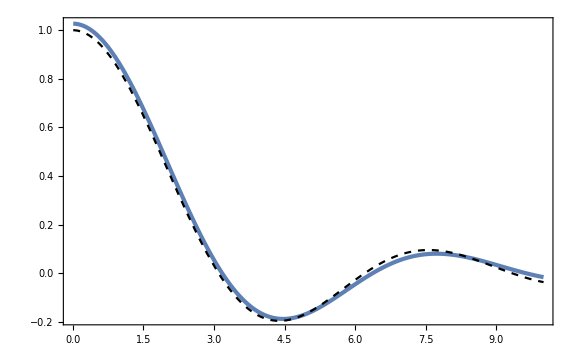

```mathematica
Show[ListPlot[biasList],Plot[ζx[x,k3tb],{x,10^-2,10},PlotStyle->{Black,Dashed}]]
```

```mathematica
Cpk[x_]=2/3(1-(1+x Sqrt[As]ν2 ζp[x,k3tb]))/.{As->5 10^-3,ν2->8};
Cbias[x_]=2/3(1-(1+x Sqrt[As]ν2 bpint[x]))/.{As->5 10^-3,ν2->8};
```

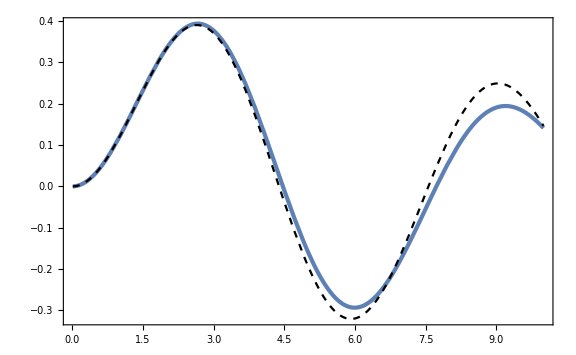

```mathematica
Plot[{Cbias[x],Cpk[x]},{x,10^-2,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed}}]
```

## Lognormal σ^2=10^-1

```mathematica
npeak=16;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/10) π)

```mathematica
R3//N
```

2.19025

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/5)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];]
```

{10.7768,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
```

```mathematica
s2b=10^-1;
```

```mathematica
Normal[Series[Sinc''[E^lnk x]+2/(x E^lnk)Sinc'[E^lnk x],{x,0,0}]]
```

-1

```mathematica
1/x^2 D[(x^2 D[(b''[x]+2/x b'[x]), x]), x]//Simplify
```

(4 b^(3)[x])/x+b^(4)[x]

```mathematica
Normal[Series[Sinc''''[E^lnk x]+4/(x E^lnk)Sinc'''[E^lnk x],{x,0,0}]]
```

1

1

```mathematica
Lapb0=-kpeak^2 NIntegrate[E^(2lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
LapLapb0=kpeak^4 NIntegrate[E^(4lnk)1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
k3tb=Sqrt[σ2/σ4]Sqrt[-LapLapb0/Lapb0]
```

-0.161597674133744942791483575238

0.0371768569093574033209316104054

0.67032004603563930074443292515

```mathematica
bias[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[Sinc[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
bp[x_]:=(-σ1^2/σ2^2 Lapb0)^-1 NIntegrate[E^lnk Sinc'[E^lnk x] 1/Sqrt[2π s2b] Exp[-lnk^2/(2s2b)]Sqrt[calPz[lnk]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[biasList=ParallelTable[{x,bias[x]},{x,10^-2,10,10^-2}];
bpList=ParallelTable[{x,bp[x]},{x,10^-2,10,10^-2}];]
```

{3.69907,Null}

```mathematica
biasint[x_]=Interpolation[biasList][x];
bpint[x_]=Interpolation[bpList][x];
```

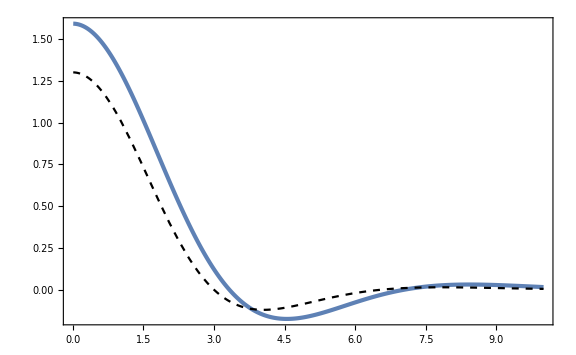

```mathematica
Show[ListPlot[biasList],Plot[ζx[x,k3tb],{x,10^-2,10},PlotStyle->{Black,Dashed}]]
```

```mathematica
Lbcheck[x_]=biasint''[x]+2/x biasint'[x];
Lpkcheck[x_]=D[D[ζx[x,k3tb], x], x]+2/x D[ζx[x,k3tb], x];
```

```mathematica
LLbcheck[x_]=Lbcheck''[x]+2/x Lbcheck'[x];
LLpkcheck[x_]=Lpkcheck''[x]+2/x Lpkcheck'[x];
```

```mathematica
Lbcheck[10^-2]
Lpkcheck[10^-2]
```

-1.82209614201266020946951

-1.8220961508792434790528

```mathematica
LLbcheck[10^-2]
LLpkcheck[10^-2]
```

5.435681311094415513

5.436978998701751013

```mathematica
Cpk[x_]=2/3(1-(1+x Sqrt[As]ν2 ζp[x,k3tb]))/.{As->5 10^-3,ν2->8};
Cbias[x_]=2/3(1-(1+x Sqrt[As]ν2 bpint[x]))/.{As->5 10^-3,ν2->8};
```

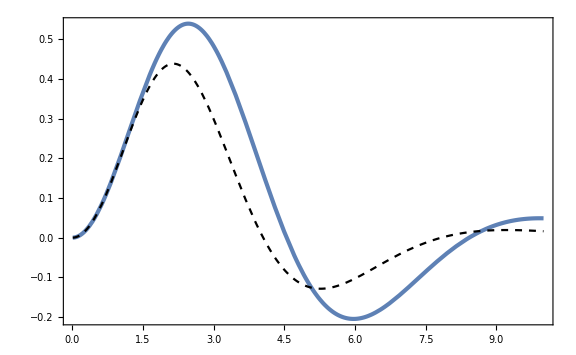

```mathematica
Plot[{Cbias[x],Cpk[x]},{x,10^-2,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed}}]
```